```mathematica
(*визуализация функций двух переменных*)
```

```mathematica
f[x_, y_]:=Cos[x+y]Cos[x-y]
```

```mathematica
Plot3D[f[x,y], {x, -5, 5}, {y, -5, 5}]
```

-Graphics3D-

```mathematica
h1 = ContourPlot[f[x,y], {x, -5, 5}, {y, -5, 5}, PlotLegends->Automatic, Contours->40]
```

-Graphics-

```mathematica
FindMaximum[f[x,y], {{x,3}, {y,0}}]
```

{1.,{x→3.14159,y→0.}}

```mathematica
g = Grad[f[x,y], {x,y}]
```

{-Cos[x+y] Sin[x-y]-Cos[x-y] Sin[x+y],Cos[x+y] Sin[x-y]-Cos[x-y] Sin[x+y]}

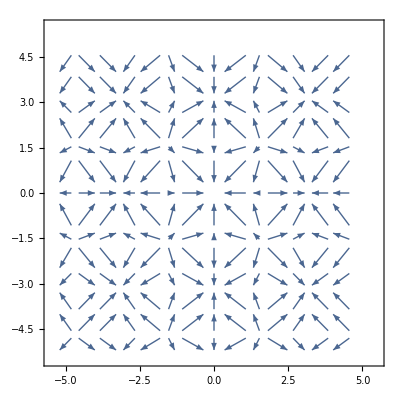

```mathematica
h2 = VectorPlot[g, {x, -5, 5}, {y, -5, 5}, PlotLegends->Automatic]
```

```mathematica
Show[h1,h2]
```

-Graphics-

```mathematica
(*Неявно заданная функция многих переменных*)
```

```mathematica
ContourPlot3D[x^2+y^2/4 + z^2/6==1, {x,-5,5}, {y, -5, 5}, {x, -5, 5}]
```

ContourPlot3D::glims: Range specifications {x,-5,5}, {y,-5,5}, and {x,-5,5} contain the same iteration variable.

General::stop: Further output of ContourPlot3D::glims will be suppressed during this calculation.

ContourPlot3D[x^2+y^2/4+z^2/6==1,{x,-5,5},{y,-5,5},{x,-5,5}]

```mathematica
(*Параметрически заданная функция двух переменных *)
```

```mathematica
ParametricPlot3D[{Sin[t1]Cos[t2], Cos[t2]t1, Sin[t2]t1}, {t1,0,10}, {t2, 0 , 20}]
```

-Graphics3D-

```mathematica
(*Параметрически заданная Кривая в R^3*)
```

```mathematica
ParametricPlot3D[{Sin[t1]t1, Cos[t1]t1, t1}, {t1,0,10}]
```

-Graphics3D-

```mathematica
(*3D*)
```

```mathematica
Graphics3D[{Red, Ball[{0,0,0}, 1]}, Axes->True]
```

-Graphics3D-

```mathematica
(*Области *)
```

```mathematica
r1 = ImplicitRegion[x^2+y^2 ≤ 1, {x,y}]
```

ImplicitRegion[x^2+y^2≤1,{x,y}]

```mathematica
RegionPlot[r1]
```

-Graphics-

```mathematica
r2 = ImplicitRegion[y>-x, {x,y}];
```

```mathematica
r3 = RegionIntersection[r1,r2];
```

```mathematica
RegionPlot[r3]
```

-Graphics-

```mathematica
(*RegionUnion, RegionDifference*)
```

```mathematica
Plot3D[f[x,y], {x,y}∈r3]
```

-Graphics3D-

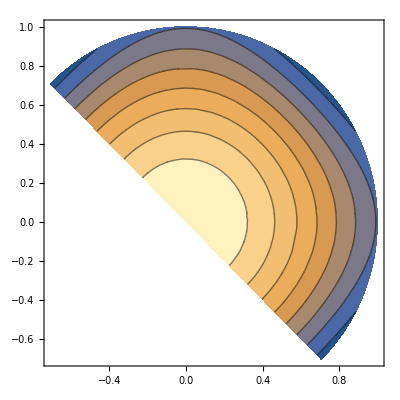

```mathematica
ContourPlot[f[x,y], {x,y}∈r3]
```

```mathematica
NMaximize[{f[x,y], {x,y}∈r3}, {x,y}]
```

{1.,{x→1.85844×10^-9,y→5.055×10^-9}}

```mathematica
NMinimize[{f[x,y], {x,y}∈r3}, {x,y}]
```

{0.155944,{x→0.707107,y→0.707107}}

```mathematica
(*Работа со списками и массивами *)
```

```mathematica
Clear[a, b]
```

```mathematica
l = {a,1,b,2}
```

{a,1,b,2}

```mathematica
l[[2]]
```

1

```mathematica
Part[l,2]
```

1

```mathematica
l1 = {{1,2}, {2,3}}
```

{{1,2},{2,3}}

```mathematica
l1[[2,2]]
```

3

```mathematica
l2 = l1//Flatten
```

{1,2,2,3}

```mathematica
l + l2
```

{1+a,3,2+b,5}

```mathematica
l*l2
```

{a,2,2 b,6}

```mathematica
Sqrt[l]
```

{√a,1,√b,√2}

```mathematica
Sin[l]
```

{Sin[a],Sin[1],Sin[b],Sin[2]}

```mathematica
l^2
```

{a^2,1,b^2,4}

```mathematica
Clear[g]
```

```mathematica
Map[g, l]
```

{g[a],g[1],g[b],g[2]}

```mathematica
g/@l
```

{g[a],g[1],g[b],g[2]}

```mathematica
l+2
```

{2+a,3,2+b,4}

```mathematica
Apply[Plus, l]
```

3+a+b

```mathematica
Plus @@ l
```

3+a+b

```mathematica
(*преобразование Списков:*)
```

```mathematica
l
```

{a,1,b,2}

```mathematica
Insert[l, q, 3]
```

{a,1,q,b,2}

```mathematica
l
```

{a,1,b,2}

```mathematica
Delete[l,3]
```

{a,1,2}

```mathematica
l
```

{a,1,b,2}

```mathematica
Insert[l, q, {{3}, {5}}]
```

{a,1,q,b,2,q}

```mathematica
Append[l,0]
```

{a,1,b,2,0}

```mathematica
Prepend[l,9]
```

{9,a,1,b,2}

```mathematica
(*Изменяют массив*)
```

```mathematica
AppendTo[l,11]
```

{a,1,b,2,11}

```mathematica
PrependTo[l,-11]
```

{-11,a,1,b,2,11}

```mathematica
First[l]
```

-11

```mathematica
Last[l]
```

11

```mathematica
Rest[l]
```

{a,1,b,2,11}

```mathematica
Most[l]
```

{-11,a,1,b,2}

```mathematica
Take[l, {2,4}]
```

{a,1,b}

```mathematica
l⟦2;;4⟧
```

{a,1,b}

```mathematica
Length[l]
```

6

```mathematica
l
```

{-11,a,1,b,2,11}

```mathematica
Dimensions[l1]
```

{2,2}

```mathematica
l1
```

{{1,2},{2,3}}

```mathematica
Drop[l, {2,4}]
```

{-11,2,11}

```mathematica
TakeDrop[l, {2,4}]
```

{{a,1,b},{-11,2,11}}

```mathematica
Nest[g, l ,3]
```

g[g[g[{-11,a,1,b,2,11}]]]

```mathematica
l
```

{-11,a,1,b,2,11}

```mathematica
RotateLeft[l,1]
```

{a,1,b,2,11,-11}

```mathematica
RotateRight[l,1]
```

{11,-11,a,1,b,2}

```mathematica
Riffle[l,t]
```

{-11,t,a,t,1,t,b,t,2,t,11}

```mathematica
Reverse@l
```

{11,2,b,1,a,-11}

```mathematica
f[x_]:=If[x < 0, True, False]
```

```mathematica
f[a]
```

If[a<0,True,False]

```mathematica
f[1]
```

False

```mathematica
f[-1]
```

True

```mathematica
l
Select[l,f]
```

{-11,a,1,b,2,11}

{-11}

```mathematica
Select[l, #<0&]
```

{-11}

```mathematica
(#1^2+2#2)&[a,b]
```

a^2+2 b

```mathematica
10^#&[3]
```

1000

```mathematica
10^#&/@Range[5]
```

{10,100,1000,10000,100000}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Select[l, MatchQ[__?Negative]]
```

{-11}

```mathematica
y[x_Symbol, z__Integer]:=Apply[Times, x^{z}]
```

```mathematica
y[x,2]
```

x^2

```mathematica
y[x,2,3]
```

x^5

```mathematica
l
```

{-11,a,1,b,2,11}

```mathematica
l/._?Negative:>o
```

{o,a,1,b,2,11}

```mathematica
l/._?f:>o
```

{o,a,1,b,2,11}

```mathematica
Min[l]
```

Min[-11,a,b]

```mathematica
Max[l]
```

Max[11,a,b]

```mathematica
Sort[Range[5], Greater]
```

{5,4,3,2,1}

```mathematica
RandomInteger[{-5,5}, 15]
```

{4,3,-5,5,-5,4,0,-5,4,0,0,4,3,1,2}

```mathematica
RandomReal[{-5,5}, 15]
```

{1.4751,-3.35268,-2.12008,0.412715,-2.87009,0.49759,2.33405,2.63555,-4.94791,3.62794,2.55085,4.67755,1.24358,0.688477,1.87123}

```mathematica
RandomReal[{-5,5}, {15,3}]
```

{{-1.78676,-2.16791,-3.20237},{3.51347,-2.44534,1.67689},{0.529417,-3.843,-4.22752},{-1.80557,-4.30612,-4.26959},{-2.90089,3.90865,-4.55561},{-4.32457,1.22069,-2.89945},{-1.80311,-3.50259,-3.97905},{-3.00979,-0.00847671,4.20694},{-3.31512,-1.39938,1.04029},{4.94338,3.56618,1.02807},{-0.371536,-3.58731,1.72857},{-0.900562,-1.69348,4.55341},{0.88857,-3.56949,0.736473},{-0.876633,2.95274,-2.14927},{-2.56067,-2.50627,-2.19602}}

```mathematica
l
```

{-11,a,1,b,2,11}

```mathematica
Position[l,a]
```

{{2}}